## Extraction of the Regge poles

The extraction of the Regge poles has been done by hands, the summary is in my internship report. Therefore I start straight the computations of the Regge poles from equation 3.18 (pol = p_k(s)) :

```mathematica
kmax:=100;
Clear[k, d, s, pol];
P = ParallelTable[1/(n!)NorlundB[n, s+1, s+1]//Simplify,{n, 0, kmax}];
pol = ParallelTable[
2^(2k)∑_(n1=0)^k (-s)^n1(∑_(m=0)^Floor[n1/2 ] Pochhammer[s+(d-1)/2+m-k, Floor[k/2]-m]/(m!(n1-2m)!2^(2m+n1)))P[[k-n1+1]]//Simplify,
{k, 0, kmax},
Method->"FinestGrained"
]
```

In order to get the polynomes without recomputing everything:

```mathematica
pol =
```

To arrive to the integral expression of section 4.1, a resumation was necessary. This was done like this (p = Floor(k/2)) :

```mathematica
∑_(n=0)^p Pochhammer[s+(d-1)/2+n , p-n]/(2^(4n)n!)((s+2p) t)^(2n)//FullSimplify
```

Gamma[-1/2+d/2+p+s] Hypergeometric0F1Regularized[1/2 (-1+d)+s,1/16 (2 p+s)^2 t^2]-(16^-p ((2 p+s) t)^(2 p) (-1+HypergeometricPFQ[{1},{1+p,-1/2+d/2+p+s},1/16 (2 p+s)^2 t^2]))/Gamma[1+p]

Only the first term will give a non zero value in the integral I have to compute explaining why I only kept this one. I then do a quick check that the integral expression is exact  by plotting for various value of s and d the plot in k:

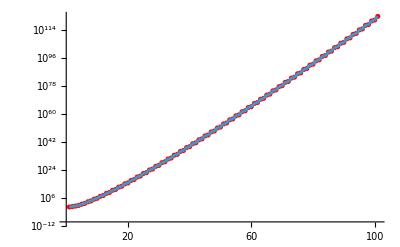

```mathematica
dd = 5;
ss = 0;
intVal = Table[((-1)^k 2^(2k)Gamma[ss+(dd-1)/2])/(k!√Pi Gamma[ss+(dd-2)/2])Pochhammer[ss+(dd-1)/2, Floor[k/2]]NIntegrate[(1-u^2)^(ss+(dd-4)/2)NorlundB[k, ss+k+1, ((ss+k)/2)(1-u)], {u, -1,1}],{k, 0, kmax}];
polVal = Table[pol[[kk+1]]/.d->dd/.s->ss+kk,{kk, 0, kmax}];

Show[
ListPlot[polVal, ScalingFunctions->{"Linear","Log"}, PlotStyle->Red],
ListLinePlot[intVal, ScalingFunctions->{"Linear","Log"}]
]
```

## Asymptotic of p_k(s+k)

The first graph I want to take a look at is p_k(k) in function of d.

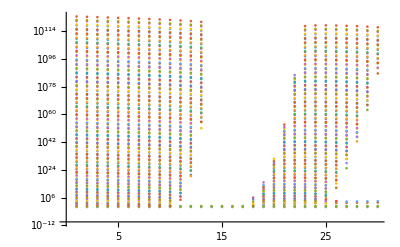

```mathematica
Clear[dd, kk];
polkD = Table[pol[[kk+1]]/.d->dd/.s->kk,{kk, 0, kmax}, {dd, 1, 30}];
ListPlot[
polkD 
,ScalingFunctions->{"Linear","Log"}]
```

From this graph, two things are clear, after d = 10, the positivity isn’t verified. Also, for large k, the positivity might not depend to much on the dimension. However, the very steep slope of the first limit of points may imply a very slow convergence of an approximation where d can be neglected. The asymptotic may still be interesting and the expression we got in section 4.2 is numerically quite good :

{9.80594,6.30997,4.03203,3.31416,2.44137,2.18153,1.73716,1.61267,1.34752,1.27674,1.10176,1.05662,0.932881,0.901676,0.809663,0.786799,0.715725,0.698236,0.641683,0.627862,0.581781,0.570584,0.532299,0.523047,0.490722,0.482956,0.455289,0.448686,0.424729,0.419055,0.398101,0.393181,0.374693,0.370394,0.353954,0.350173,0.335455,0.33211,0.318853,0.315878,0.303871,0.301213,0.290286,0.2879,0.27791,0.275762,0.266592,0.26465,0.256201,0.254441,0.246629,0.245028,0.237783,0.236324,0.229585,0.228251,0.221965,0.220743,0.214866,0.213743,0.208235,0.207202,0.202029,0.201076,0.196207,0.195327,0.190735,0.189921,0.185584,0.184829,0.180724,0.180024,0.176133,0.175482,0.171789,0.171182,0.167672,0.167106,0.163764,0.163237,0.160051,0.159558,0.156518,0.156057,0.153153,0.15272,0.149943,0.149537,0.146877,0.146497,0.143948,0.14359,0.141145,0.140808,0.13846,0.138143,0.135886,0.135588,0.133416,0.133135}

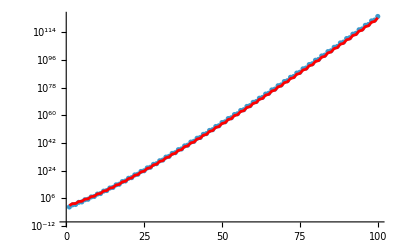

```mathematica
Clear[s, ss, dd];
polK = Table[pol[[k+1]]/.s->s+k,{k,1,100}];
ss=10;
dd=10;
approx = Table[((1)2^(2(ss+k)+dd-3))/(√Pi)Gamma[ss+(dd-1)/2+Floor[k/2]]/(k+ss)^(ss+(dd-2)/2)1/(√(2 Pi)dd/2)Exp[-(ss+k) Log[1+1/(ss+k)]]/((ss+k+1)Log[ss+k]),{k, 1, 100}];
valPol = Evaluate[polK/.s->ss/.d->dd];
approx/valPol//N
Show[
ListPlot[valPol,ScalingFunctions->"Log"],
ListLinePlot[approx2, ScalingFunctions->"Log", PlotStyle->Red]
]
```